# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.05, 0.1,0.2, 0.5, 1};
κs = {0.05, 0.1, 0.2,0.5, 1};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
```

{{λ→0.05,κ→0.05},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.1,κ→0.05},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.2,κ→0.05},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.5,κ→0.05},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→1,κ→0.05},{λ→1,κ→0.1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1}}

### Find which parameter values have a Jacobian with imaginary eigenvalues

```mathematica
eigenvectors = Table[{{(1+√(1-4 κ λ))/(2 κ),1},{-(-1+√(1-4 κ λ))/(2 κ),1}}/.p, {p, params}]
eigenvalues = Table[{1/2 (1-√(1-4 κ λ)),1/2 (1+√(1-4 κ λ))}/.p ,{p,params}]
```

{{{19.9499,1},{0.0501256,1}},{{9.94975,1},{0.0502525,1}},{{4.94949,1},{0.0505103,1}},{{1.94868,1},{0.0513167,1}},{{0.947214,1},{0.0527864,1}},{{19.8995,1},{0.100505,1}},{{9.89898,1},{0.101021,1}},{{4.89792,1},{0.102084,1}},{{1.89443,1},{0.105573,1}},{{0.887298,1},{0.112702,1}},{{19.798,1},{0.202041,1}},{{9.79583,1},{0.204168,1}},{{4.79129,1},{0.208712,1}},{{1.7746,1},{0.225403,1}},{{0.723607,1},{0.276393,1}},{{19.4868,1},{0.513167,1}},{{9.47214,1},{0.527864,1}},{{4.43649,1},{0.563508,1}},{{1.,1},{1.,1}},{{0.5+0.5 ⅈ,1},{0.5-0.5 ⅈ,1}},{{18.9443,1},{1.05573,1}},{{8.87298,1},{1.12702,1}},{{3.61803,1},{1.38197,1}},{{1.+1. ⅈ,1},{1.-1. ⅈ,1}},{{1/2 (1+ⅈ √3),1},{1/2 (1-ⅈ √3),1}}}

{{0.00250628,0.997494},{0.00502525,0.994975},{0.0101021,0.989898},{0.0256584,0.974342},{0.0527864,0.947214},{0.00502525,0.994975},{0.0101021,0.989898},{0.0204168,0.979583},{0.0527864,0.947214},{0.112702,0.887298},{0.0101021,0.989898},{0.0204168,0.979583},{0.0417424,0.958258},{0.112702,0.887298},{0.276393,0.723607},{0.0256584,0.974342},{0.0527864,0.947214},{0.112702,0.887298},{0.5,0.5},{0.5-0.5 ⅈ,0.5+0.5 ⅈ},{0.0527864,0.947214},{0.112702,0.887298},{0.276393,0.723607},{0.5-0.5 ⅈ,0.5+0.5 ⅈ},{1/2 (1-ⅈ √3),1/2 (1+ⅈ √3)}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x

```mathematica
Table[1/(2κ)+((1+κ) λ)/(2κ)/.p, {p, params}]
```

{10.525,5.275,2.65,1.075,0.55,11.05,5.55,2.8,1.15,0.6,12.1,6.1,3.1,1.3,0.7,15.25,7.75,4.,1.75,1.,20.5,10.5,5.5,2.5,3/2}

```mathematica
{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]]
```

{{20.5,1/2},{1/2,0.525}}

#### Also choose initial width for the steady-state width of each parameter pair

{{20.5,1/2},{1/2,0.525}}

{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,2]==0}

ElementMesh[{{-15.,15.},{2.,15.}},{QuadElement[<15770>]}]

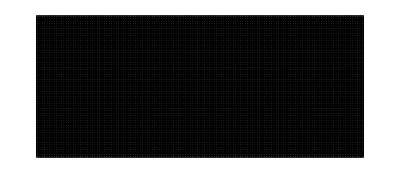

```mathematica
xf=15;
xstar = 2;
icPos = {5, 5};
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]] 
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcs = {P[-xf, xh]==0,
           P[xf, xh]==0,
           P[x, xf]==0,
           P[x, xstar]==0
}

Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Rectangle[{-xf, xstar}, {xf, xf}],MaxCellMeasure->0.025 ]
mesh["Wireframe"]
```

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bcs],
                                   P,Element[{x, xh}, mesh], 
Method->"FiniteElement"];
Return[(P/.N[[1]])];
]
```

```mathematica
solsSS=MapThread[NDSolverParams, {params, icSS}];
solsIc0=MapThread[NDSolverParams, {params, ic0}];
```

```mathematica
fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];
fluxIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

```mathematica
fieldSS = Table[-Grad[sol[x, xh],{x,xh}],{sol,solsSS}];
fieldIc0 = Table[-Grad[sol[x, xh],{x,xh}],{sol,solsIc0}];
```

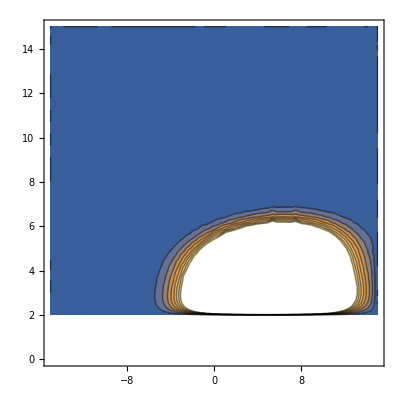

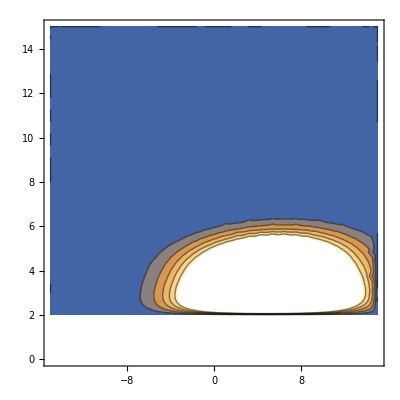

```mathematica
cSS =ContourPlot[solsSS[[1]][x, xh], {x, -xf, xf}, {xh, 0, xf}];
cIc0 =ContourPlot[solsIc0[[1]][x, xh], {x, -xf, xf}, {xh, 0, xf}];
Show[cSS]
Show[cIc0]
```

```mathematica
XSS = Table[f[x,xstar], {f, fluxSS}];
XIc0 = Table[f[x,xstar], {f, fluxIc0}];
```

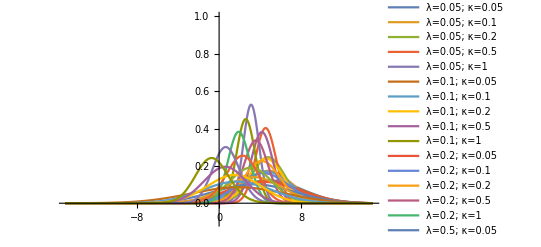

```mathematica
Plot[XSS, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

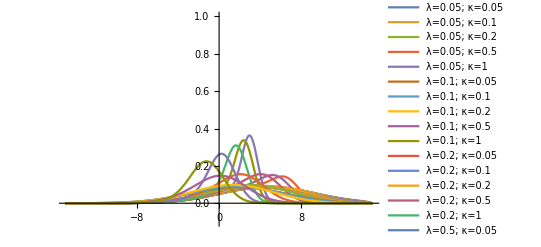

```mathematica
Plot[XIc0, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
normsSS = Table[NIntegrate[xp, {x, -10, 10}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 10}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 10}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;
```

{0.9416771392,0.9866849708,1.000415674,1.003292585,0.9992394328,0.9427296541,0.9870643353,1.00028535,1.003255015,1.000530713,0.944701414,0.9876646741,0.9999758948,1.00286293,1.000504289,0.9494248516,0.9886985471,0.9988835676,1.000616177,0.9960725561,0.9481897024,0.9884566599,0.9968284286,0.9958319658,0.9862894534}

{4.194973078,4.691402169,4.791567874,4.571486674,3.132520289,4.045167224,4.522638253,4.586735566,4.206782621,2.626317393,3.746029618,4.187227531,4.188670121,3.596906212,1.962676417,2.855216808,3.201371014,3.073081323,2.21013234,0.7188877759,1.426628109,1.630950113,1.410921819,0.519601101,-0.6298974933}

{8.97157809,5.1109449,2.6022798,0.92385787,0.56978919,9.30391468,5.3472911,2.7564777,1.0517204,0.76887537,10.0119567,5.85580934,3.1074344,1.3920779,1.0805296,12.4074006,7.61839333,4.38631342,2.46655632,1.76925451,16.3983767,11.0490158,6.8941586,4.07700261,2.68874086}

```mathematica
normsIc0 = Table[NIntegrate[xp, {x, -10, 10}, WorkingPrecision->10], {xp, XIc0}]
meansIc0= Table[NIntegrate[xp*x, {x, -10, 10}, WorkingPrecision->10], {xp, XIc0}]
secondIc0 = Table[NIntegrate[xp*x*x, {x, -10, 10}, WorkingPrecision->10], {xp, XIc0}];
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

{0.87011277,0.8725260102,0.8793905204,0.980727695,0.9791818125,0.8775066023,0.8812526528,0.8930315587,0.9824587989,0.9819069385,0.8910544251,0.8970094533,0.915860816,0.9829537878,0.9814332605,0.9224087929,0.9313833054,0.9528626205,0.9811662234,0.9756779341,0.9481897024,0.9560128209,0.968708303,0.976148818,0.9647035642}

{3.284473706,3.296128612,3.331387247,3.699255228,1.98605666,3.219754829,3.234549961,3.288040543,3.30346017,1.588418584,3.075510482,3.092154961,3.155558655,2.698813339,1.021681407,2.540636008,2.531776612,2.47665023,1.404957775,-0.1133792633,1.426628109,1.33629321,1.074562917,-0.1408998356,-1.359744431}

{13.4382724,13.4122623,13.3589606,11.0927578,4.32778247,13.5339946,13.4838457,13.3795426,9.92204795,3.85773714,13.7594065,13.6578081,13.4136932,8.76225055,3.42961115,14.6580827,14.3664885,13.5075854,7.58022316,3.10385924,16.3983767,15.7263063,13.923959,7.38003791,3.38228384}

```mathematica
λs = { 0.05, 0.1, 0.2, 0.5, 1};
σs = {0.05, 0.1, 0.2, 0.5, 1};
grid = Flatten[Table[{l, s}, {l, λs}, {s, σs}], 1];
params
```

{{λ→0.05,κ→0.05},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.1,κ→0.05},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.2,κ→0.05},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.5,κ→0.05},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→1,κ→0.05},{λ→1,κ→0.1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1}}

```mathematica
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];
varArrayIc0 = ArrayReshape[varsIc0, {5, 5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5, 5}];
diffArrayIc0 = ArrayReshape[diffIc0, {5, 5}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ xstar,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, σs}];
```

```mathematica
ArrayPlot[varArraySS, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArraySS]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[diffArraySS, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-